# Classification of P’s

At least at the moment, we are restricting our attention to P matrices which have certain symmetries. Given the number of reference outcomes(n), the rank of P (r), and the inverse depolarizing parameter (α), we require:
	1) ∀ i, j: P_ij ≥ 0
	2) ∀j:∑_iP_ij = 1
	3) P = P^T
	4) ∀ i: P_ii= const.
	5) Eigenvalues of P: {1, 1/α, ..., 0, ..., 0}, where 1/α is repeated r-1 times.
In low dimensions, this strongly restricts the possible P’s. Here we classify P matrices up to n=4. It would desirable to do this perhaps up to n=6, the first case where there is a quantum 3-design to be found. 

We can also analytically solve for the state-spaces (we consider only the case of simple A here)!

## Preliminaries

```mathematica
ConstructΦ[n_, α]:=With[{β=(1-α)/n}, α IdentityMatrix[n] + β ConstantArray[1, {n,n}]];
ConstructV [n_]:= Table[KroneckerDelta[i,j]KroneckerDelta[i,k],{i, 1, n}, {j, 1, n}, {k, 1, n}];
ConstructA[n_, α_]:=With[{η=(-1+α)/(n (1+α))},  Table[η(KroneckerDelta[i,j]-KroneckerDelta[i,k]-KroneckerDelta[j,k]),{i, 1, n}, {j, 1, n}, {k, 1, n}]];
ConstructB[n_,α_, χ_]:=With[{V = ConstructV[n], A = ConstructA[n, α]}, FullSimplify[Table[Sum[(V[[i,j,k]]-A[[i,j,k]])χ[[k]],{k,1, n}], {i, 1, n}, {j, 1, n}]]];
ConstructC[n_, α_, P_, χ_]:=With[{Φ=ConstructΦ[n, α], B = ConstructB[n, α, χ]},FullSimplify[P.Φ.B.P.Φ]];
```

```mathematica
ConstructEmbedding[n_]:=Transpose[SingularValueDecomposition[IdentityMatrix[n]-ConstantArray[1, {n,n}]/n][[3]]][[1;;n-1]];
Embed[χ_]:= With[{n = Length[χ],F = ConstructEmbedding[Length[χ]]}, FullSimplify[F.(χ-1/n)]];
Unembed[λ_]:= With[{n = Length[λ]+1,F = ConstructEmbedding[Length[λ]+1]}, FullSimplify[(Transpose[F].λ) + 1/n]];
```

## n=2

```mathematica
n=2;
```

```mathematica
Pn2 = {{p[1], 1-p[1]}, {1-p[1], p[1]}}; Pn2//MatrixForm
```

(p[1] | 1-p[1]
1-p[1] | p[1])

```mathematica
Eigenvalues[Pn2]
```

{1,-1+2 p[1]}

## r=1

```mathematica
soln = Solve[-1+2 p[1]==0,p[1]]
```

{{p[1]→1/2}}

```mathematica
Pn2r1 = FullSimplify[Pn2/.soln[[1]]] ; Pn2r1// MatrixForm
```

(1/2 | 1/2
1/2 | 1/2)

Obviously, for r=1, this is pretty boring! And this is generally true, due to the stochastic condition. If we demand r=1, we end up with (1/n) J, where J is the matrix of all 1’s.

## r=2

```mathematica
soln = Solve[-1+2 p[1]==1/α,p[1]]
```

{{p[1]→(1+α)/(2 α)}}

```mathematica
Pn2r2 = FullSimplify[Pn2/.soln[[1]]] ; Pn2r2// MatrixForm
```

((1+α)/(2 α) | (-1+α)/(2 α)
(-1+α)/(2 α) | (1+α)/(2 α))

```mathematica
Reduce[Pn2r2>=0]
```

α≤-1||α≥1

Naturally, we want α ≥ 1. So now we have all the P’s with n=2, r=2 as a function of α.

### State-space

We first define λ: components of a state embedded into n-1 dimensions. Then get the unembedded version χ, and construct the C matrix.

```mathematica
λ = Array[x, {n-1}];
χ = Unembed[λ];
Cn2r2=ConstructC[n, α,Pn2r2, χ]; Cn2r2//MatrixForm
```

((1+α-2 √2 α x[1])/(2+2 α) | 1/2-1/(1+α)
1/2-1/(1+α) | (1+α+2 √2 α x[1])/(2+2 α))

The condition for validity is that all the eigenvalues of C are non-negative. We also ensure that the components of the probability vector are in [0,1], and that α ≥ 1.

```mathematica
Reduce[{Eigenvalues[Cn2r2]>=0, 0 <= χ <=1, α>=1}, λ]
```

(α==1&&-1/(√2)≤x[1]≤1/(√2))||(α>1&&-(√(1/α))/(√2)≤x[1]≤(√(1/α))/(√2))

Indeed, the first case, when α = 1, corresponds to the classical simplex.

```mathematica
{Unembed[{-1/(√2)}], Unembed[{1/(√2)}]}
```

{{1,0},{0,1}}

So let’s consider the embedded points corresponding to: 1) the vertices of the simplex, 2) the reference states, and 3) the bounds on the state-space.

```mathematica
SimplexVectors = {-1/(√2), 1/(√2)};
ValidRegion = {-(√(1/α))/(√2),(√(1/α))/(√2) };
ReferenceVectors =FullSimplify[Flatten[Table[Embed[Pn2r2[[i]]], {i, 1, n}]]]
```

{-1/(√2 α),1/(√2 α)}

Below we plot in 1D the simplex vectors in red, the reference states in green, and the bounds on the state space in blue. You can drag the slider to change the value of α.

```mathematica
Manipulate[Show[{ContourPlot[{ x==-1/(√2), x==1/(√2)},{x,-1,1},{y,-1,1}, ContourStyle->{Red}],ContourPlot[{ x==-(√(1/α))/(√2), x==(√(1/α))/(√2)},{x,-1,1},{y,-1,1}, ContourStyle->{Blue}],ContourPlot[{ x==-1/(√2 α), x==1/(√2 α)},{x,-1,1},{y,-1,1}, ContourStyle->{Green}]}], {α, 1, 100}]
```

## n=3

```mathematica
n=3;
```

```mathematica
Pn3= {{p[1], p[2], 1-p[1]-p[2]}, {p[2], p[1],1-p[1]-p[2]}, {1-p[1]-p[2], 1-p[1]-p[2], p[1]}};Pn3//MatrixForm
```

(p[1] | p[2] | 1-p[1]-p[2]
p[2] | p[1] | 1-p[1]-p[2]
1-p[1]-p[2] | 1-p[1]-p[2] | p[1])

But also the last column must sum to 1.

```mathematica
soln =Solve[Total[Pn3[[All, 3]]]==1, p[2]]
```

{{p[2]→1/2 (1-p[1])}}

Thus we really only have 1 free parameter.

```mathematica
Pn3= {{p[1], p[2], 1-p[1]-p[2]}, {p[2], p[1],1-p[1]-p[2]}, {1-p[1]-p[2], 1-p[1]-p[2], p[1]}};
Pn3 = FullSimplify[Pn3/.soln[[1]]]; Pn3 //MatrixForm
```

(p[1] | 1/2 (1-p[1]) | 1/2 (1-p[1])
1/2 (1-p[1]) | p[1] | 1/2 (1-p[1])
1/2 (1-p[1]) | 1/2 (1-p[1]) | p[1])

```mathematica
Eigenvalues[Pn3]
```

{1,1/2 (-1+3 p[1]),1/2 (-1+3 p[1])}

Since the latter two eigenvalues are the same, we have only two cases r=1, and r=3.

## r=3

```mathematica
soln = Solve[1/2 (-1+3 p[1])==1/α]
```

{{p[1]→(2+α)/(3 α)}}

```mathematica
Pn3r3 = FullSimplify[Pn3/.soln[[1]]]; Pn3r3//MatrixForm
```

((2+α)/(3 α) | (-1+α)/(3 α) | (-1+α)/(3 α)
(-1+α)/(3 α) | (2+α)/(3 α) | (-1+α)/(3 α)
(-1+α)/(3 α) | (-1+α)/(3 α) | (2+α)/(3 α))

```mathematica
Reduce[Pn2r2>=0]
```

α≤-1||α≥1

Again there’s really just one choice up to α.

### State-space

```mathematica
λ = Array[x, {n-1}];
χ = Unembed[λ];
Cn3r3=ConstructC[n, α,Pn3r3, χ]; Cn3r3//MatrixForm
```

(-(-8-4 α+3 √2 (1+5 α) x[1]+√6 x[2]+5 √6 α x[2])/(18 (1+α)) | ((-1+α) (4-3 √2 x[1]+√6 x[2]))/(18 (1+α)) | -((-1+α) (-2+√6 x[2]))/(9 (1+α))
((-1+α) (4-3 √2 x[1]+√6 x[2]))/(18 (1+α)) | (2 (2+α)+√6 (1+5 α) x[2])/(9 (1+α)) | ((-1+α) (4+3 √2 x[1]+√6 x[2]))/(18 (1+α))
-((-1+α) (-2+√6 x[2]))/(9 (1+α)) | ((-1+α) (4+3 √2 x[1]+√6 x[2]))/(18 (1+α)) | (8+4 α+3 √2 (1+5 α) x[1]-√6 x[2]-5 √6 α x[2])/(18 (1+α)))

To save computation, let’s specialize to a particular case of α.

```mathematica
Fixedα = 10;
eigs =Eigenvalues[Cn3r3/.{α->Fixedα}];
cons =Reduce[{eigs>=0, 0 <= χ <=1}, λ]
```

(x[1]==Root-0.133Root[31752+10577893 #1^2-869070400 #1^4+9370240000 #1^6&,2]-0.13259963940804817&&x[2]==Root[8-603 #1^2+660 √6 #1^3-603 x[1]^2-1980 √6 #1 x[1]^2&,1])||(Root-0.133Root[31752+10577893 #1^2-869070400 #1^4+9370240000 #1^6&,2]-0.13259963940804817<x[1]<Root0.133Root[31752+10577893 #1^2-869070400 #1^4+9370240000 #1^6&,3]0.13259963940804817&&Root[8-603 #1^2+660 √6 #1^3-603 x[1]^2-1980 √6 #1 x[1]^2&,1]≤x[2]≤Root[8-603 #1^2+660 √6 #1^3-603 x[1]^2-1980 √6 #1 x[1]^2&,2])||(x[1]==Root0.133Root[31752+10577893 #1^2-869070400 #1^4+9370240000 #1^6&,3]0.13259963940804817&&x[2]==Root[8-603 #1^2+660 √6 #1^3-603 x[1]^2-1980 √6 #1 x[1]^2&,1])

Again we plot the embedded simplex vectors in red, the reference states in green, and the valid region in blue.

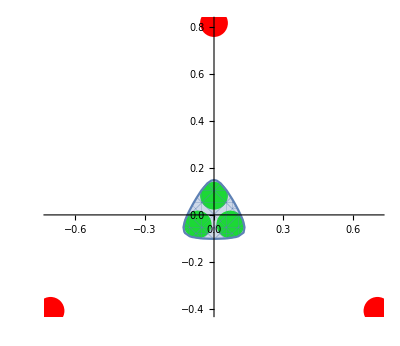

```mathematica
SimplexVectors=Table[Embed[UnitVector[n,i]],{i, 1, n}];
ReferenceVectors =Table[Embed[Pn3r3[[i]]/.{α->Fixedα}],{i, 1, n}];Show[{ListPlot[SimplexVectors, PlotStyle->{Red, PointSize[0.05]}], ListPlot[ReferenceVectors, PlotStyle->{Green, PointSize[0.05]}],RegionPlot[cons,{x[1], -1, 1}, {x[2], -1, 1}]}, AspectRatio->Automatic]
```

## n=4

```mathematica
n=4;
```

```mathematica
Pn4 =  {{p[1],p[2],p[3],1-p[1]-p[2]-p[3]},{p[2],p[1], p[4], 1-p[1]-p[2]-p[4]},{p[3],p[4],p[1],1-p[1]-p[3]-p[4]},{1-p[1]-p[2]-p[3],1-p[1]-p[2]-p[4],1-p[1]-p[3]-p[4],p[1]}}; Pn4//MatrixForm
```

(p[1] | p[2] | p[3] | 1-p[1]-p[2]-p[3]
p[2] | p[1] | p[4] | 1-p[1]-p[2]-p[4]
p[3] | p[4] | p[1] | 1-p[1]-p[3]-p[4]
1-p[1]-p[2]-p[3] | 1-p[1]-p[2]-p[4] | 1-p[1]-p[3]-p[4] | p[1])

```mathematica
soln =Solve[Total[Pn4[[All, 4]]]==1, p[4]]
```

{{p[4]→1-p[1]-p[2]-p[3]}}

```mathematica
Pn4 =  {{p[1],p[2],p[3],1-p[1]-p[2]-p[3]},{p[2],p[1], p[4], 1-p[1]-p[2]-p[4]},{p[3],p[4],p[1],1-p[1]-p[3]-p[4]},{1-p[1]-p[2]-p[3],1-p[1]-p[2]-p[4],1-p[1]-p[3]-p[4],p[1]}}; 
Pn4 =FullSimplify[ Pn4/. soln[[1]]];Pn4//MatrixForm
```

(p[1] | p[2] | p[3] | 1-p[1]-p[2]-p[3]
p[2] | p[1] | 1-p[1]-p[2]-p[3] | p[3]
p[3] | 1-p[1]-p[2]-p[3] | p[1] | p[2]
1-p[1]-p[2]-p[3] | p[3] | p[2] | p[1])

## r=2

```mathematica
{a,b,c,d}=Eigenvalues[Pn4]
```

{1,-1+2 p[1]+2 p[2],1-2 p[2]-2 p[3],-1+2 p[1]+2 p[3]}

```mathematica
Reduce[{c==0, d==0}, p[3]]
```

p[1]==p[2]&&p[3]==1/2-p[2]

```mathematica
Pn4r2a= FullSimplify[Pn4/.{p[2]->p[1], p[3]->1/2-p[1]}]; Pn4r2a//MatrixForm
```

(p[1] | p[1] | 1/2-p[1] | 1/2-p[1]
p[1] | p[1] | 1/2-p[1] | 1/2-p[1]
1/2-p[1] | 1/2-p[1] | p[1] | p[1]
1/2-p[1] | 1/2-p[1] | p[1] | p[1])

```mathematica
Eigenvalues[Pn4r2a]
```

{1,0,0,-1+4 p[1]}

```mathematica
soln = Solve[-1+4 p[1]==1/α]
```

{{p[1]→(1+α)/(4 α)}}

```mathematica
Pn4r2 = FullSimplify[Pn4r2a/.soln[[1]]]; Pn4r2//MatrixForm
```

((1+α)/(4 α) | (1+α)/(4 α) | (-1+α)/(4 α) | (-1+α)/(4 α)
(1+α)/(4 α) | (1+α)/(4 α) | (-1+α)/(4 α) | (-1+α)/(4 α)
(-1+α)/(4 α) | (-1+α)/(4 α) | (1+α)/(4 α) | (1+α)/(4 α)
(-1+α)/(4 α) | (-1+α)/(4 α) | (1+α)/(4 α) | (1+α)/(4 α))

```mathematica
Reduce[Pn4r2>=0]
```

α≤-1||α≥1

#### State-space

```mathematica
λ = Array[x, {n-1}];
χ = Unembed[λ];
Cn4r2=ConstructC[n, α,Pn4r2, χ]; Cn4r2//MatrixForm
```

((3+α (3-6 √2 x[1]-2 √6 x[2]+4 √3 x[3]))/(24 (1+α)) | (3+α (3-6 √2 x[1]-2 √6 x[2]+4 √3 x[3]))/(24 (1+α)) | (-1+α)/(8 (1+α)) | (-1+α)/(8 (1+α))
(3+α (3-6 √2 x[1]-2 √6 x[2]+4 √3 x[3]))/(24 (1+α)) | (3+α (3-6 √2 x[1]-2 √6 x[2]+4 √3 x[3]))/(24 (1+α)) | (-1+α)/(8 (1+α)) | (-1+α)/(8 (1+α))
(-1+α)/(8 (1+α)) | (-1+α)/(8 (1+α)) | (3+α (3+6 √2 x[1]+2 √6 x[2]-4 √3 x[3]))/(24 (1+α)) | (3+α (3+6 √2 x[1]+2 √6 x[2]-4 √3 x[3]))/(24 (1+α))
(-1+α)/(8 (1+α)) | (-1+α)/(8 (1+α)) | (3+α (3+6 √2 x[1]+2 √6 x[2]-4 √3 x[3]))/(24 (1+α)) | (3+α (3+6 √2 x[1]+2 √6 x[2]-4 √3 x[3]))/(24 (1+α)))

```mathematica
Fixedα = 2;
eigs =Eigenvalues[Cn4r2/.{α->Fixedα}];
Consn4r2 =Reduce[{eigs>=0, 0 <= χ <=1}, λ];
```

```mathematica
eigs//MatrixForm
```

(0
0
1/36 (9-√3 √(3+96 x[1]^2+64 √3 x[1] x[2]+32 x[2]^2-64 √6 x[1] x[3]-64 √2 x[2] x[3]+64 x[3]^2))
1/36 (9+√3 √(3+96 x[1]^2+64 √3 x[1] x[2]+32 x[2]^2-64 √6 x[1] x[3]-64 √2 x[2] x[3]+64 x[3]^2)))

```mathematica
Length[Consn4r2]
```

26

```mathematica
SimplexVectors=Table[Embed[UnitVector[n,i]],{i, 1, n}];
ReferenceVectors =Table[Embed[Pn4r2[[i]]/.{α->Fixedα}],{i, 1, n}];
Show[{RegionPlot3D[Consn4r2, {x[1], -1, 1}, {x[2], -1, 1}, {x[3], -1, 1}, PerformanceGoal->"Quality", PlotPoints->25,MaxRecursion->5,PlotStyle->{Opacity[0.5]}],ListPointPlot3D[SimplexVectors, PlotStyle->{Red, PointSize[0.05],AspectRatio->1}], ListPointPlot3D[ReferenceVectors, PlotStyle->{Green, PointSize[0.05]}]}]
```

-Graphics3D-

## r=3

```mathematica
{a,b,c,d}=Eigenvalues[Pn4]
```

{1,-1+2 p[1]+2 p[2],1-2 p[2]-2 p[3],-1+2 p[1]+2 p[3]}

```mathematica
soln =Solve[d==0, p[3]]
```

{{p[3]→1/2 (1-2 p[1])}}

```mathematica
Pn4r3a=FullSimplify[Pn4/.soln[[1]]];Pn4r3a// MatrixForm
```

(p[1] | p[2] | 1/2-p[1] | 1/2-p[2]
p[2] | p[1] | 1/2-p[2] | 1/2-p[1]
1/2-p[1] | 1/2-p[2] | p[1] | p[2]
1/2-p[2] | 1/2-p[1] | p[2] | p[1])

```mathematica
Eigenvalues[Pn4r3a]
```

{1,0,2 (p[1]-p[2]),-1+2 p[1]+2 p[2]}

```mathematica
soln =Solve[2 (p[1]-p[2])==-1+2 p[1]+2 p[2]]
```

{{p[2]→1/4}}

```mathematica
Pn4r3b = FullSimplify[Pn4r3a/.soln[[1]]]; Pn4r3b//MatrixForm
```

(p[1] | 1/4 | 1/2-p[1] | 1/4
1/4 | p[1] | 1/4 | 1/2-p[1]
1/2-p[1] | 1/4 | p[1] | 1/4
1/4 | 1/2-p[1] | 1/4 | p[1])

```mathematica
Eigenvalues[Pn4r3b]
```

{1,0,1/2 (-1+4 p[1]),1/2 (-1+4 p[1])}

```mathematica
soln =Solve[1/2 (-1+4 p[1])==1/α, p[1]]
```

{{p[1]→(2+α)/(4 α)}}

```mathematica
Pn4r3=FullSimplify[Pn4r3b/.soln[[1]]]; Pn4r3//MatrixForm
```

((2+α)/(4 α) | 1/4 | (-2+α)/(4 α) | 1/4
1/4 | (2+α)/(4 α) | 1/4 | (-2+α)/(4 α)
(-2+α)/(4 α) | 1/4 | (2+α)/(4 α) | 1/4
1/4 | (-2+α)/(4 α) | 1/4 | (2+α)/(4 α))

```mathematica
Reduce[Pn4r3>=0]
```

α≤-2||α≥2

### State-space

```mathematica
λ = Array[x, {n-1}];
χ = Unembed[λ];
Cn4r3=ConstructC[n, α,Pn4r3, χ]; Cn4r3//MatrixForm
```

(1/24 (3-9 √2 x[1]-5 √6 x[2]+(3+6 √2 x[1]+6 √6 x[2])/(1+α)-2 √3 x[3]) | (α (3-6 √2 x[1]-2 √6 x[2]+4 √3 x[3]))/(24 (1+α)) | 1/24 (3-9/(1+α)+3 √2 x[1]-√6 x[2]+2 √3 x[3]) | -(α (-3+4 √6 x[2]+4 √3 x[3]))/(24 (1+α))
(α (3-6 √2 x[1]-2 √6 x[2]+4 √3 x[3]))/(24 (1+α)) | (6+3 α-3 √2 (-1+α) x[1]-√6 x[2]+√6 α x[2]+2 √3 x[3]+10 √3 α x[3])/(24 (1+α)) | (α (3+4 √6 x[2]+4 √3 x[3]))/(24 (1+α)) | 1/24 (3-9/(1+α)-3 √2 x[1]+√6 x[2]-2 √3 x[3])
1/24 (3-9/(1+α)+3 √2 x[1]-√6 x[2]+2 √3 x[3]) | (α (3+4 √6 x[2]+4 √3 x[3]))/(24 (1+α)) | (6+3 α+3 √2 (-1+α) x[1]+√6 x[2]+7 √6 α x[2]-2 √3 x[3]-2 √3 α x[3])/(24 (1+α)) | (α (3+6 √2 x[1]+2 √6 x[2]-4 √3 x[3]))/(24 (1+α))
-(α (-3+4 √6 x[2]+4 √3 x[3]))/(24 (1+α)) | 1/24 (3-9/(1+α)-3 √2 x[1]+√6 x[2]-2 √3 x[3]) | (α (3+6 √2 x[1]+2 √6 x[2]-4 √3 x[3]))/(24 (1+α)) | (6+3 α+3 √2 (1+3 α) x[1]-√6 x[2]-3 √6 α x[2]+2 √3 x[3]-6 √3 α x[3])/(24 (1+α)))

```mathematica
Fixedα = 3;
eigs =Eigenvalues[Cn4r3/.{α->Fixedα}];
Consn4r3 =Reduce[{eigs>=0, 0 <= χ <=1}, λ];
```

$Aborted

```mathematica
SimplexVectors=Table[Embed[UnitVector[n,i]],{i, 1, n}];
ReferenceVectors =Table[Embed[Pn4r3[[i]]/.{α->Fixedα}],{i, 1, n}];
Show[{RegionPlot3D[Consn4r3, {x[1], -1, 1}, {x[2], -1, 1}, {x[3], -1, 1}, PerformanceGoal->"Quality", PlotPoints->25,MaxRecursion->5,PlotStyle->{Opacity[0.5]}],ListPointPlot3D[SimplexVectors, PlotStyle->{Red, PointSize[0.05],AspectRatio->1}], ListPointPlot3D[ReferenceVectors, PlotStyle->{Green, PointSize[0.05]}]}]
```

## r=4

```mathematica
{a,b,c,d}=Eigenvalues[Pn4]
```

{1,-1+2 p[1]+2 p[2],1-2 p[2]-2 p[3],-1+2 p[1]+2 p[3]}

```mathematica
soln=Solve[{-1+2 p[1]+2 p[2]==1/α, 1-2 p[2]-2 p[3]==1/α, -1+2 p[1]+2 p[3]==1/α}]
```

{{p[1]→(3+α)/(4 α),p[2]→(-1+α)/(4 α),p[3]→(-1+α)/(4 α)}}

```mathematica
Pn4r4 = FullSimplify[Pn4/.soln[[1]]]; Pn4r4//MatrixForm
```

((3+α)/(4 α) | (-1+α)/(4 α) | (-1+α)/(4 α) | (-1+α)/(4 α)
(-1+α)/(4 α) | (3+α)/(4 α) | (-1+α)/(4 α) | (-1+α)/(4 α)
(-1+α)/(4 α) | (-1+α)/(4 α) | (3+α)/(4 α) | (-1+α)/(4 α)
(-1+α)/(4 α) | (-1+α)/(4 α) | (-1+α)/(4 α) | (3+α)/(4 α))

```mathematica
Reduce[Pn4r4>=0]
```

α≤-3||α≥1

### State-space

```mathematica
λ = Array[x, {n-1}];
χ = Unembed[λ];
Cn4r4=ConstructC[n, α,Pn4r4, χ]; Cn4r4//MatrixForm
```

(-(-9-3 α+6 √2 (1+3 α) x[1]+2 √6 x[2]+6 √6 α x[2]+2 √3 x[3]+6 √3 α x[3])/(24 (1+α)) | -((-1+α) (-3+3 √2 x[1]+√6 x[2]-2 √3 x[3]))/(24 (1+α)) | -((-1+α) (-3+3 √2 x[1]-√6 x[2]+2 √3 x[3]))/(24 (1+α)) | -((-1+α) (-3+2 √6 x[2]+2 √3 x[3]))/(24 (1+α))
-((-1+α) (-3+3 √2 x[1]+√6 x[2]-2 √3 x[3]))/(24 (1+α)) | (3+α+2 √3 x[3]+6 √3 α x[3])/(8+8 α) | ((-1+α) (3+2 √6 x[2]+2 √3 x[3]))/(24 (1+α)) | ((-1+α) (3+3 √2 x[1]-√6 x[2]+2 √3 x[3]))/(24 (1+α))
-((-1+α) (-3+3 √2 x[1]-√6 x[2]+2 √3 x[3]))/(24 (1+α)) | ((-1+α) (3+2 √6 x[2]+2 √3 x[3]))/(24 (1+α)) | (9+3 α+4 √6 (1+3 α) x[2]-2 √3 x[3]-6 √3 α x[3])/(24 (1+α)) | ((-1+α) (3+3 √2 x[1]+√6 x[2]-2 √3 x[3]))/(24 (1+α))
-((-1+α) (-3+2 √6 x[2]+2 √3 x[3]))/(24 (1+α)) | ((-1+α) (3+3 √2 x[1]-√6 x[2]+2 √3 x[3]))/(24 (1+α)) | ((-1+α) (3+3 √2 x[1]+√6 x[2]-2 √3 x[3]))/(24 (1+α)) | (9+3 α+6 √2 (1+3 α) x[1]-2 √6 x[2]-6 √6 α x[2]-2 √3 x[3]-6 √3 α x[3])/(24 (1+α)))

```mathematica
Fixedα = 2;
eigs =Eigenvalues[Cn4r4/.{α->Fixedα}];
Consn4r4 =Reduce[{eigs>=0, 0 <= χ <=1}, λ];
```

$Aborted

```mathematica
SimplexVectors=Table[Embed[UnitVector[n,i]],{i, 1, n}];
ReferenceVectors =Table[Embed[Pn4r4[[i]]/.{α->Fixedα}],{i, 1, n}];
Show[{RegionPlot3D[Consn4r4, {x[1], -1, 1}, {x[2], -1, 1}, {x[3], -1, 1}, PerformanceGoal->"Quality", PlotPoints->25,MaxRecursion->5,PlotStyle->{Opacity[0.5]}],ListPointPlot3D[SimplexVectors, PlotStyle->{Red, PointSize[0.05],AspectRatio->1}], ListPointPlot3D[ReferenceVectors, PlotStyle->{Green, PointSize[0.05]}]}]
```